# 2. Norms

## Norms

A norm ||.|| is just a way to measure how big something (a vector or a matrix in our course) is.  Any norm needs to satisfy the following
	1) ||x||≥0  and ||x||=0 implies x is zero.
	2) ||x+y||≤||x||+||y||
	3) ||α x||=|α| ||x||

## Vector Norms: ||x(||)_p

Useful vector norms are ||x(||)_p^p=∑_(i=1)^m |x_i|^p with p≥1. This includes the familiar Euclidean norm p=2, and in the limit as p→∞ the pessimists norm||x(||)_∞=max_i |x_i|. All are available in most software package.  I would hope the default is always the 2 norm!

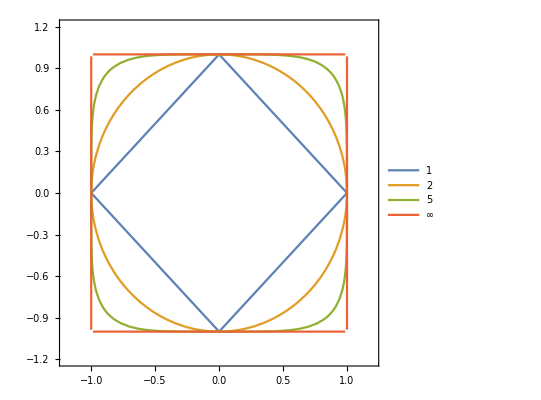

```mathematica
p=5;
ContourPlot[ {
Norm[{x1,x2},1]==1,Norm[{x1,x2},2]==1,Norm[{x1,x2},p]==1,Norm[{x1,x2},∞]==1},{x1,-1.2,1.2},{x2,-1.2,1.2},
PlotLegends->{1,2,p,∞}]
```

## Matrix Norms: ||A||

There are lots of useful norms for A∈ℂ^(m×n)! Different packages have different defaults! You should always check what you are computing!

### Frobenius Norm: ||A(||)_F

One useful norm is the Hilbert-Schmidt or Frobenius norm 
	||A(||)_F^2=∑_(i=1)^m ∑_(j=1)^n|A_(i,j)|^2=∑_(j=1)^n ||a_j(||)_2^2

### Induced Vector Norms: ||A(||)_p

Each vector p-norm defines (fancy word induces) a norm for matrices A∈ℂ^(m×n) via 
	||A(||)_(m,n)=max_(x≠0) (||A.x(||)_(m))/(||x(||)_(n))=max_(||x(||)_(n)=1) ||A.x(||)_(m)
The matrix norm induced by the two norm is the most common of these. It is the default in Mathematica.

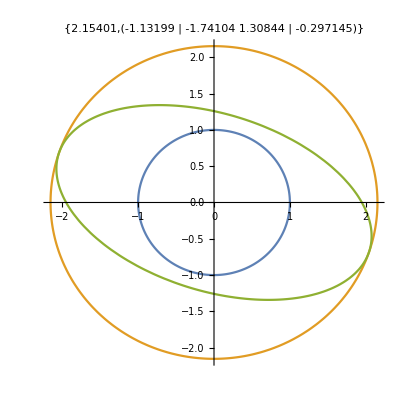

```mathematica
A=RandomReal[{-2,2},{2,2}];
s=Norm[A];
ParametricPlot[{{Cos[θ],Sin[θ]},s{Cos[θ],Sin[θ]},A.{Cos[θ],Sin[θ]}},{θ,0,2π},PlotRange->All,
PlotLabel->{s,A}]
```

## Norm Examples

We want to be able to guarantee that things are small under certain conditions.  For example, we would like to ensure that a matrix Q  is very close to orthogonal or that the residual of a QR decomposition ||A-Q.R|| is tiny.  We need to get comfortable with these norms.

### 3.1 Induced Norm

```mathematica
Clear[UCirc]
UCirc[p_]:=Table[ Map[Sign[#] Abs[#]^(2/p)&,{Cos[θ],Sin[θ]}],{θ,0, 2π,π/32}];
```

```mathematica
A=({{1.0, 2}, {0, 2}}); ps={1,1.5,2,2.5,5,125};
FNorm=Norm[A,"Frobenius"];
CPic=ContourPlot[
Norm[{x1,x2}],{x1,-FNorm,FNorm},{x2,-FNorm,FNorm},ContourLabels->All, ContourShading->None];
TabView[
Table[p->(
OrigPoints=UCirc[p];
NumPoints=Length[OrigPoints];
Show[CPic,
Epilog->{PointSize[0.015],Blue,Line[OrigPoints],
Table[x=OrigPoints⟦i⟧;{Hue[i/NumPoints],Point[x],Arrow[{x,A.x}]},{i,NumPoints}]
}]),
{p,ps}]]
```

123456

### 3.2 Diagonal Matrices

The unit spheres in the various vector norms have the same pattern in ℝ^m with m>2.  I can only draw pics with m=3.

```mathematica
in=Date[]
ContourPlot3D[ {Norm[{x1,x2,x3},1]==1,Norm[{x1,x2,x3},1.5]==1,Norm[{x1,x2,x3},2]==1,Norm[{x1,x2,x3},2.5]==1,Norm[{x1,x2,x3},25]==1},
{x1,0,1.1},{x2,0,1.1},{x3,0,1.1},
PlotLegends->{1,1.5,2,2.5,25},
ContourStyle->Opacity[0.5]]
Date[]-in
```

{2022,1,19,16,20,46.2687838}

-Graphics3D-

{0,0,0,0,0,9.9430085}

A diagonal matrix (with diagonals d_1,…,d_m) simply scales the basis directions. For instance, the image of the m-dimensional unit sphere (p=2) is an m-dimensional ellipsoid (lined up with the coordinate axes) with semi-axis lengths |d_1|,…,|d_m|.

```mathematica
A=SparseArray[Band[{1,1}]->{3,2,0.5},{3,3}];
ParametricPlot3D[ {{Cos[θ]Sin[ϕ],Sin[θ]Sin[ϕ],Cos[ϕ]},A.{Cos[θ]Sin[ϕ],Sin[θ]Sin[ϕ],Cos[ϕ]}},
{θ,0, 2π},{ϕ,0, π},
PlotLabel->{Norm[A,1],Norm[A,2],Norm[A,∞]},
BoxRatios->Automatic,PlotStyle->Opacity[0.5]]
```

In fact, for a diagonal matrix ||D(||)_p=max_(1≤i≤m) |d_i| for any 1≤p≤∞.

### 3.3 Formula for 1-Norm

For A∈ℝ^(m×n) we need to maximize||A.x(||)_1 for x∈ℝ^n with ||x(||)_1=1: the diamond!  Think of A a columns 
	A=[a_1|a_2|…|a_n]
then
	||A.x(||)_1=||∑_(j=1)^n x_j a_j(||)_1≤∑_(j=1)^n ||x_j a_j(||)_1=∑_(j=1)^n |x_j| ||a_j(||)_1≤max_(1≤j≤n)||a_j||.
But ||A.e_j(||)_1=||a_j|| so ||A(||)_1=max_(1≤j≤n) ||a_j||.

### 3.4 Formula for ∞-Norm

For A∈ℝ^(m×n) we need to maximize||A.x(||)_∞ for x∈ℝ^n with ||x(||)_∞=1: the block!  Think of A as rows (or if you want Aᵀ as columns) 
	A=(a_1^*
-
a_2^*
-
⋮
-
a_m^*)
and basically repeat the argument from above. 
	||A.x(||)_∞=max_(1≤i≤m) |x.a_i^*|≤max_(1≤i≤m) (∑_(j=1)^n |x_j| |(a_i^*)_j|)≤max_(1≤i≤m) (∑_(j=1)^n |(a_i^*)_j|)=max_(1≤i≤m) ||a_i^*||
and  ||A(||)_∞=max_(1≤i≤m) ||a_i^*|| since a corner matches this estimate.

### Holder (1/p+1/q=1) and Cauchy-Schwarz (p=q=2) Inequalities

The CS inequality is the special case 
	|x.y|≤||x(||)_2||y(||)_2	
of the Holder inequality
	|x.y|≤||x(||)_p||y(||)_q.
You already know a proof of the CS inequality since 
	(x.y)/(||x(||)_2||y(||)_2)=cos(α)
and |cos(α)|≤1.  We are going to skip a Holder proof.

### Example 3.5/3.6 2-Norm of rank one matrix A=u⊗v

Remember if A=u⊗v the A_ij=u_i v_j and as a result A.x=u (v.x) so 
	||A.x(||)_2=||u(||)_2|v.x|≤||u(||)_2||v(||)_2||x(||)_2
and A.v/||v(||)_2=u so the bound is obtained when x=v/||v(||)_2.  So
	||u⊗v(||)_2=||u(||)_2||v(||)_2

### Induced Norms of Matrix Products A.B

Since for any induced norm 
	||A.B.x||≤||A||||B.x||≤||A||||B||||x||
we have 
	||A.B||≤||A||||B||.
There is no reason for this to be an equality!

### Rotational Invariance: Qᵀ.Q=I

The Euclidean 2-norm and the matrix norm induced by the 2-norm are rotationally invariant
	||x(||)_2=||Q_1.x(||)_2  and ||A(||)_2=||Q_1.A.Q_2(||)_2
In addition, since the Frobenius norm is constructed from (row or column) 2-Norms
	||A(||)_F=||Q_1.A.Q_2(||)_F